# Caso 1: David Franco Veiga

```mathematica
<< "/home/david/Documentos/RRT/RandomData.m"
```

## Apartados 1 y 2

### 1. Desarrollar un sistema generador de números aleatorios basado en un generador lineal congruencial mixto que siga una distribución uniforme entre [0,1]. 2. Probar el generador y demostrar mediante un histograma la bondad del generador.

```mathematica
RandomData[]
```

0.773033

```mathematica
max=10000;
```

```mathematica
array=Table[RandomData[],{i,max}];(**)
```

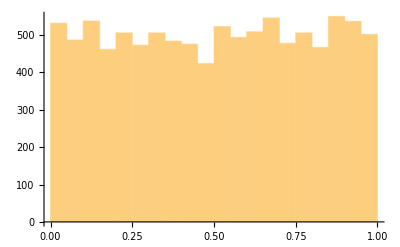

```mathematica
Histogram[array]
```

## Apartado 3

### Implementar el método de transformada inversa para obtener una distribución aleatoria exponencial de tiempo entre llegadas 1/λ. Representar en un histograma los valores obtenidos.

```mathematica
lambda=100;
```

```mathematica
arrayExp=Table[RandomExp[lambda],{i,max}];(*RandomExp es una funcion de Armando que ya tiene en cuenta lo de la dist uniforme*)
```

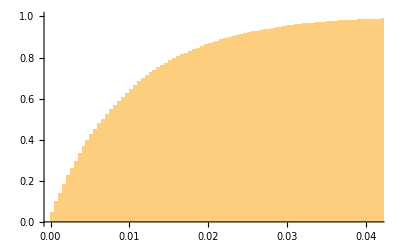

```mathematica
Histogram[arrayExp,lambda,CDF]
```

```mathematica
(*Para pedir ayuda de una funcion*)
?RandomData`*
```

```mathematica
(*Trunca un array entre 50 y 100*)
arrayExp[[50;;100]];
```

```mathematica
(*La media tiene que salir proxima a 1/lambda*)
mean=Mean[arrayExp[[1;;100]]]
```

0.0106145

## Apartado 4

## Desarrollar un simulador de una cola M/M/1 con tasa λ de llegadas y μ de servicio. Representar en un diagrama que evolucione en el tiempo el número de usuarios en el sistema.

Escaleras

```mathematica
nmax=10000;
```

```mathematica
InterArr=Table[RandomExp[lambda],nmax];
```

```mathematica
InterArr[[1;;100]];
```

```mathematica
Arriv=Accumulate[InterArr];
```

```mathematica
mu=200;
ServTime=Table[RandomExp[mu],nmax];
ServTime[[1;;11]]
```

{0.011496,0.00132299,0.00762595,0.00709864,0.00770619,0.00313332,0.0135309,0.00331535,0.00631672,0.00398033,0.0180775}

```mathematica
(*Module es para organizar la funcion, para que las variables tengan caracter local.
*Primero se definen la variables, luego se inicializan, y finalmente se ejecuta el If.
*El /@ indica que se esta usando un Map[]
*El # es para acceder a cada elemento de la variable arrivals dentro del Map[]
*El &  es para definir una funcion pura, se suele usar con un Map[]  
*)
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&/@arrivals]
```

```mathematica
Departures=FifoSchedulling[Arriv,ServTime];
```

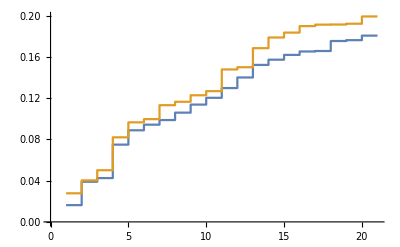

```mathematica
ListStepPlot[{Arriv[[1;;20]],Departures[[1;;20]]}]
```

```mathematica
(*Usar Map[] (sirve para recorrer una lista) en lugar de For[]*)
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
Map[
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&,
arrivals]]
```

```mathematica
(*MM/#colas/#usuarios: si hay dos colas y 3 usuarios, cada usuarios ira a una cola,y el tercero se queda esperando*)
```

```mathematica
Manipulate[
ListStepPlot[{Arriv[[origin;;origin+width]],Departures[[origin;;origin+width]]}]
, {origin,1,1000-width,1},{width,10,50,1}
]
```

Part::take: Cannot take positions 1 through 11 in Arriv.

Part::take: Cannot take positions 1 through 11 in Departures.

Montañas (David)

```mathematica
(*Montañitas: Departures - Arriv*)
(* Necesitas una funcion que te compare los tiempos de llegada con los de salida, de manera que cuando el tiempo de salida sea superior al de llegada, se sume un usuario a la cola*)
(*Hacerlo de esta forma (con For[])es un poco locura, el mas complejo, y tarda mas en simular, a parte de que el algoritmo no esta del todo bien*)
```

```mathematica
(*UsuariosCola[arrivals_, departures_]:= (
Module[{users=0,n=1,i=1,time=0,montana={}},
For[n=1,n<nmax,n++,
For[i=1,i<(nmax-n),i++,
If[departures[[n]]> arrivals[[n+i]], 
users++;time=arrivals[[n+i]];AppendTo[montana,{users,time}],
users--;time=departures[[n]];AppendTo[montana,{users,time}];Break[]
]
]
];
montana
]
) *)
```

```mathematica
(*UsuariosCola[arrivals_, departures_]:= (
Module[{users=0,n=1,i=1,last=0,time=0,montana={}},
For[n=1,n<nmax,n+=last,
For[i=1,i<(nmax-n),i++,
If[ arrivals[[n+i]]<departures[[n]], 
users++;time=arrivals[[n+i]];AppendTo[montana,{users,time}],
users--;time=departures[[n]];AppendTo[montana,{users,time}];last=i;Break[]
]
]
];
montana
]
)
*)
```

Montaña (Armando)

```mathematica
ArrivEvent[lst_]:=Map[{#,1}&,lst];(*Se regenera la lista pero poniendo 1 para saber que se suma a la cola*)
DeparturesEvent[lst_]:=Map[{#,-1}&,lst]; (*Se regenera la lista pero poniendo -1 para saber que se resta a la cola*)
ArrivEvent[Arriv];
DeparturesEvent[Departures];
(*Join[]: concatena los arrais ArrivEvent[Arriv] y DeparturesEvent[Departures]; Sort[]: ordena los elementos de menor a mayor*)
EventList=Sort[Join[ArrivEvent[Arriv],DeparturesEvent[Departures]]];
(*Flatten[]: desagrupa*)
DrawMontain[lst_]:=
Module[{n=0,lastTime=0},
Flatten[Map[{{lastTime,n},{lastTime=#[[1]],If[#[[2]]==1,n++,n--]}}&,lst],1]
]
```

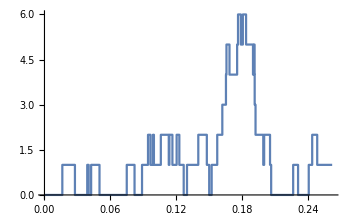

```mathematica
listStates=DrawMontain[EventList];
ListLinePlot[listStates[[1;;100]]]
```

```mathematica
listStates[[1;;6]]
```

{{0,0},{0.016271,0},{0.016271,1},{0.027767,1},{0.027767,0},{0.0389757,0}}

## Apartado 5

## Representar el tiempo medio de espera en el sistema normalizado por μ para diferentes valores de ρ. Hacerlo con la curva teórica y representar los puntos obtenidos en las simulaciones.

```mathematica
ro=lambda/mu;
```

```mathematica
media= Mean[Departures-Arriv];
```

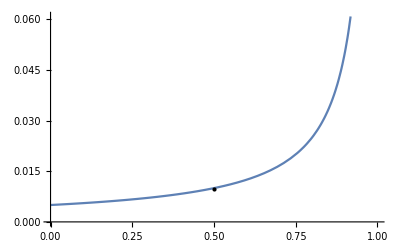

```mathematica
Show[Plot[tespera=1/((1-ro)*mu),{ro,0,1}, AxesOrigin->{0,0}],Graphics[{PointSize[Large],Point[{ro,media}]}]]
```

```mathematica
(*Solo consigo dibujar un punto, me falta el resto de puntos*)
```

```mathematica
TesperaMedido=Departures-Arriv;
```

```mathematica
mediaTesperaMedido=Flatten[Map[{Mean[#]}&,Partition[TesperaMedido,1000]],1]
```

{0.0095736,0.00954023,0.00945418,0.00980832,0.0109826,0.010086,0.00933897,0.00883935,0.00993164,0.0099371}

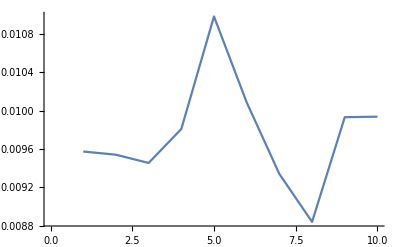

```mathematica
ListLinePlot[mediaTesperaMedido]
```

## Apartado 6

### Representar las probabilidades de estado p n de la cola M/M/1 teóricas, así como las obtenidas por simulación para diferentes puntos de ensayo. Comprobar si esa distribución coincide con la visualizada según la propiedad PASTA en los tiempos de llegada.

Simulación

```mathematica
listStates[[1;;20]]
```

{{0,0},{0.016271,0},{0.016271,1},{0.027767,1},{0.027767,0},{0.0389757,0},{0.0389757,1},{0.0402987,1},{0.0402987,0},{0.0425321,0},{0.0425321,1},{0.050158,1},{0.050158,0},{0.0750013,0},{0.0750013,1},{0.0820999,1},{0.0820999,0},{0.0889245,0},{0.0889245,1},{0.0943727,1}}

```mathematica
For[n=1; timeStates={},n<nmax,n++,AppendTo[timeStates,{listStates[[n+1]][[1]]-listStates[[n]][[1]],listStates[[n]][[2]]}]];
```

```mathematica
timeStates[[1;;20]]
```

{{0.016271,0},{0.,0},{0.011496,1},{0.,1},{0.0112087,0},{0.,0},{0.00132299,1},{0.,1},{0.0022334,0},{0.,0},{0.00762595,1},{0.,1},{0.0248433,0},{0.,0},{0.00709864,1},{0.,1},{0.00682451,0},{0.,0},{0.00544821,1},{0.,1}}

```mathematica
maxState=0;
Map[{If[#[[2]]>maxState,maxState=#[[2]]]}&,listStates];
```

```mathematica
timeState[estado_]:=
Module[{tiempo=0},
Map[{If[#[[2]]==estado, tiempo+=#[[1]]]}&,timeStates];
Return[tiempo]
]
```

```mathematica
For[state=0; probState={},state≤maxState,state++,AppendTo[probState,{state,timeState[state]/listStates[[nmax]][[1]]}]];
```

```mathematica
probState
```

{{0,0.500982},{1,0.259218},{2,0.130568},{3,0.0568874},{4,0.0307086},{5,0.0141951},{6,0.00414668},{7,0.0020125},{8,0.00112801},{9,0.000154631},{10,0.},{11,0.},{12,0.},{13,0.}}

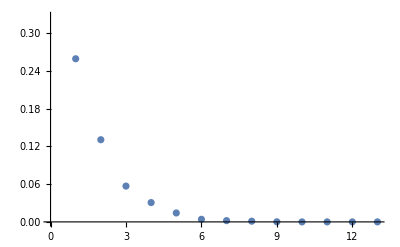

```mathematica
ListPlot[probState]
```

Teórico

```mathematica
(*probabilidadCadaEstado=(1-ro)*(ro^i);*)
```

```mathematica
probTH=Table[{n,(1-ro) ro^n//N},{n,0,maxState,1}]
```

{{0,0.5},{1,0.25},{2,0.125},{3,0.0625},{4,0.03125},{5,0.015625},{6,0.0078125},{7,0.00390625},{8,0.00195313},{9,0.000976563},{10,0.000488281},{11,0.000244141},{12,0.00012207},{13,0.0000610352}}

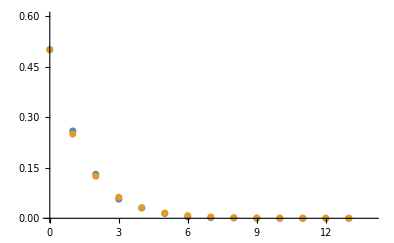

```mathematica
(*Comparativa teorica vs simulada*)
ListPlot[{probState,probTH},PlotRange->{{0,14},{0,0.6}}]
```

Propiedad PASTA

Propiedad pasta: se cuentan las veces que se ha dado un estado, muestrendo en los tiempos de llegada, y se divide entre el número de muestras totales. Es decir, se coge el ArrivalsTime y se mira en cada instante de llegada cuantos usuarios hay antes de la llegada contando el número de veces que se repite cada estado y dividiendolo entre el numero total de muestras.

```mathematica
listStates[[1;;10]]
```

{{0,0},{0.016271,0},{0.016271,1},{0.027767,1},{0.027767,0},{0.0389757,0},{0.0389757,1},{0.0402987,1},{0.0402987,0},{0.0425321,0}}

```mathematica
Arriv[[1;;10]]
```

{0.016271,0.0389757,0.0425321,0.0750013,0.0889245,0.0943727,0.0988628,0.106059,0.113876,0.120465}

```mathematica
(*acumState[state_]:=Module[{acumstate=0,i=1,n=1},For[n=1,n<nmax,n++,For[i=n,i<nmax,i++,If[Arriv[[n]]==listStates[[i]][[1]],If[listStates[[i-1]][[1]]==state,acumstate++]]]];Return[acumstate]];*)
```

```mathematica
acumState[state_]:=
Module[{acumstate=0,n},
Map[(
For[n=1,n≤ nmax,n++,
If[#==listStates[[n]][[1]],
If[listStates[[n-1]][[2]]==state,
acumstate++;
Break[]
]
]
]
)&,Arriv
];
Return[acumstate]
]
```

```mathematica
(*No esta acabado, la funcion de arriba calcula el numero de veces que se repite cada estado muestreando cuando hay una llegada. Para el estado 0, se ha sacado ese numero de repeticiones y se ha dividido entre nmax pero no da bien porque sale 0.25 en lugar de 0.5 (ro). Es una funcion muy pesada que para el estado 0 se ha tirado 3 mins y la CPU al 100%.*)
```

## Apartado 7

### Preparar las gráficas de rendimiento de colas vistas en Teoría de la información para los casos específicos que se elijan. Revisar la teoría.

No se exactamente a que se refiere este apartado,